## D_5^+ DVR Adiabatic

2/22/2019

Adiabatic treatment of D_5^+

## Average Field (Adiabatic Treatment)

### Load Package

```mathematica
Get@"~/Documents/UW/Research/H5+/Common/H5Core.m"
```

```mathematica
<<ChemTools`DVR`
<<ChemTools`Wavefunctions`
<<ChemTools`DataStructures`
<<ChemTools`Spectroscopy`
```

```mathematica
$HistoryLength=0;
Clear@@Unprotect[Out];
```

### Common

```mathematica
saMainGrid=$D5DVR["Grid"];
saGrid=saMainGrid["Points"];
```

```mathematica
d2SAPot//Clear
d2SAPot[{a_, s_}]:=
If[
With[{R1R2=RotationMatrix[-π/4].{a, s}, bounds=H5FullInterpPot[[1, 3]]},
AllTrue[R1R2, bounds[[1]]<=#<bounds[[2]]&]
],
h5PotCutVec[{a, s, Automatic, Automatic}],
$Failed
]
```

#### SA Stuff

This is misnamed as it’s really an (a,s) grid...but no energy to fix it.

```mathematica
saMainGrid=$D5DVR["Grid"];
saGrid=saMainGrid["Points"];
```

```mathematica
(*$d2SAPotMins=Import["~/Documents/UW/Research/H5+/inputs/sa_pot_mins.mx"];
d2SAPotMin[{a_, s_}]:=
d2SAPotMin[{a, s}]=
If[
With[{R1R2=RotationMatrix[-π/4].{a, s}, bounds=H5FullInterpPot[[1, 3]]},
AllTrue[R1R2, bounds[[1]]<=#<bounds[[2]]&]
],
NMinimize[
Evaluate[h5PotCut[{a, s, Automatic, Automatic}][{r1, r2}]],
{r1, r2}∈Rectangle[{.1, .1}, {2, 2}]
],
$Failed
]*)
```

```mathematica
(*potGridFunc=
 Module[
{
arr=QuantityMagnitude@H5Core`Private`H5FullPotQA,
gg
},
gg=
GatherBy[
arr, 
With[{p=#}, Round[#[[p]], .0001]&]&/@Range[3]
];
ChemTools`DataStructures`GridFunctionObject[
gg[[All, All, All, All, ;;4]],
#-Min[#]&@gg[[All, All, All, All, 5]]
]
];*)
```

```mathematica
(*Manipulate[
test=
potGridFunc@
"Compile"[{rr[[1]], rr[[2]], Automatic, Automatic},
"CoordinateTransformation"->
(Join[#[[;;2]], RotationMatrix[π/4.].#[[{4, 3}]]]&),
"Default"->10.^5
];
Join[
saGrid,
Transpose@List@test@saGrid,
2
]//ListPlot3D,
{rr, {.26, .26}, {1.8, 1.8}}
]*)
```

```mathematica
d2SAPot//Clear
d2SAPot[{a_, s_}]:=
If[
With[{R1R2=RotationMatrix[-π/4].{a, s}, bounds=H5FullInterpPot[[1, 3]]},
AllTrue[R1R2, bounds[[1]]<=#<bounds[[2]]&]
],
h5PotCutVec[{a, s, Automatic, Automatic}],
$Failed
]
```

```mathematica
d2SAPotSingles//Clear
d2SAPotSingles[{a_, s_}]:=
If[
With[{R1R2=RotationMatrix[-π/4].{a, s}, bounds=H5FullInterpPot[[1, 3]]},
AllTrue[R1R2, bounds[[1]]<=#<bounds[[2]]&]
],
h5PotCut[{a, s, Automatic, Automatic}],
$Failed
]
```

```mathematica
(*Quiet@
NMinimize[
H5FullInterpPot[r1, r2, R1, R2], 
{r1, r2, R1, R2}∈Region@Apply[Cuboid, Transpose@H5FullInterpPot[[1]]]
]*)
```

```mathematica
d2SAPotsGrid=
Flatten[
CoordinateBoundsArray[
H5FullInterpPot[[1, ;;2]],
(H5FullInterpPot[[1,1, 2]]-H5FullInterpPot[[1,1, 1]])/150
],
1
];
d2SAPotsUncoupled//Clear
d2SAPotsUncoupled[{a_, s_}]:=
d2SAPotsUncoupled[{a, s}]=
Module[
{
pot=d2SAPot[{a, s}](*d2SAPotSingles[{a, s}]*),
nmins,
r1,
r2,
vecs
},
If[pot=!=$Failed,
nmins=(* If this sucks too much just make a super refined grid over these points and use the vectorized version of the potential. That should be close-ish to right and a hell of a lot faster.
*)
MinimalBy[Thread[{d2SAPotsGrid, pot@d2SAPotsGrid}], Last][[1, 1]];
(*r1=$r1/.nmins;
r2=$r2/.nmins;*)
{r1, r2}=nmins;
{
Function[{gridList}, p[List/@gridList]]/.p->h5PotCutVec[{a, s, r1, Automatic}],
Function[{gridList}, p[List/@gridList]]/.p->h5PotCutVec[{a, s, Automatic, r2}]
},
$Failed
]
]
```

```mathematica
d2SAUncPots=AssociationMap[d2SAPotsUncoupled, saGrid];
```

```mathematica
(*Export["~/Documents/UW/Research/H5+/results/d2_outer_SA_pots_uncoupled.mx", d2SAUncPots]*)
```

~/Documents/UW/Research/H5+/results/d2_outer_SA_pots_uncoupled.mx

```mathematica
d2SAUncPots=Import@"~/Documents/UW/Research/H5+/results/d2_outer_SA_pots_uncoupled.mx";
```

```mathematica
d2SAEqPts=
Nearest[
saGrid->"Index",
{0,2.1364750560940324}
]
d2SAEqPt=d2SAEqPts[[1]];
```

{1759,1819}

#### SA Grid

```mathematica
d2SAGridObject=
Catch@$D2DVR[
"Grid",
 "PotentialOptimizationOptions"->{
"PotentialFunction"->h2SinglePot,
"OptimizedBasisSize"->25
}
];
d2SAGrid=d2SAGridObject["Grid"];
d2SAGridPts=d2SAGridObject["Points"];
```

```mathematica
rrrr=
$H2DVR[
 "PotentialOptimizationOptions"->{
"PotentialFunction"->h2SinglePot,
"OptimizedBasisSize"->25
}
];
```

### Core Data

```mathematica
(* a preload because .mx can do weird things sometimes *)
CoordinateGridObject;
GridFunctionObject;
WavefunctionsObject;
```

```mathematica
d2SAWavefunctions=Import@"~/Documents/UW/Research/H5+/results/d2_outer_SA_wfns.mx";
```

```mathematica
fullD2SAWfs=
If[#=!=$Failed,
#@"CorrectPhase"[],
#
]&/@d2SAWavefunctions;
```

#### H2 Wavefunctions

Get H_2 wavefunctions parametrized by (s, a)

```mathematica
d2SAWavefunctions=
AssociationMap[
With[{pot=d2SAPot[#]},
If[pot=!=$Failed,
$D2DVR[
"Wavefunctions",
 "PotentialEnergy"->SparseArray[Band[{1, 1}]->pot@d2SAGridPts],
"Grid"->d2SAGridObject,
"ArnoldiIterations"->5000
],
$Failed
]
]&,
saGrid
];
```

```mathematica
(*Export["~/Documents/UW/Research/H5+/results/d2_outer_SA_wfns.mx", d2SAWavefunctions]*)
```

~/Documents/UW/Research/H5+/results/d2_outer_SA_wfns.mx

```mathematica
d2SAWavefunctions=Import@"~/Documents/UW/Research/H5+/results/d2_outer_SA_wfns.mx";
```

```mathematica
d2SAValidCoords=
Complement[
Range[Length@d2SAWavefunctions],
Pick[Range[Length@d2SAWavefunctions], Values[d2SAWavefunctions], $Failed]
];
```

```mathematica
d2SAInterestingWavefunctions=
Select[d2SAWavefunctions, #=!=$Failed&];
```

#### Phase Corrections

```mathematica
rephaseThingies=
Compile[{{overlaps, _Real, 1}, {init, _Integer}, {tol, _Real}},
Module[{prev, el, ov=overlaps,swapEl=init},
Prepend[
Table[
el=ov[[i]];
If[el<-tol, swapEl=-swapEl];
swapEl,
{i, Length@ov}
],
init
]
](*,
CompilationTarget->"C"*)
];
rephaseWfns[s_, wfns_]:=
WavefunctionsObject[
{
wfns["Energies"], 
Map[Scale[#, s]&, wfns["Wavefunctions"]]
},
wfns["Grid"]
]
getPhaseCorrection//Clear
getPhaseCorrection[wfs_List, 
grid_,
state:{_Integer?IntegerQ}:{2},
 basePhase:1|-1:1,
rephase:True|False:False
]:=
Module[
{
pos,
gridPoints=grid["Points"],
cleanGrid,
cleanGridSorted,
gridReordering,
gridPositions,
reorderedWfs,
rephasedWavefunctions,
fullWfs,
overlaps,
phases,
orderComplement,
phaseVector,
newWfns
},
pos=Select[IntegerQ[#]&&#>0&]@Flatten@Position[wfs, _WavefunctionsObject, {1}];
cleanGrid=Round[grid[[pos]].RotationMatrix[π/4], .001];
cleanGridSorted=
MapIndexed[If[EvenQ[#2[[1]]], Reverse, Identity]@#&]@
SortBy[
SortBy[#, First]&/@GatherBy[cleanGrid, -#[[-1]]&], 
-#[[1, -1]]&
];
gridReordering=
Flatten@
Lookup[PositionIndex[cleanGrid], Flatten[cleanGridSorted, 1]
];
gridPositions=pos[[gridReordering]];
reorderedWfs=wfs[[gridPositions]];
fullWfs=
WavefunctionsObject[
Flatten/@
Transpose[
{#["Energies"], #["Wavefunctions"][[state]]}&/@
reorderedWfs
],
reorderedWfs[[1]]["Grid"]
];
overlaps=Developer`ToPackedArray[fullWfs@"Overlaps"[fullWfs]];
phases=rephaseThingies[Diagonal[overlaps, 1], basePhase, 0];
orderComplement=Complement[Range[Length@wfs], gridPositions];
phaseVector=
Join[phases, ConstantArray[$Failed, Length@orderComplement]][[
Ordering@Join[gridPositions, orderComplement]
]];
If[rephase,
newWfns=
MapThread[
If[#===$Failed,
#,
rephaseWfns[#, #2] 
]&,
{
phaseVector,
wfs
}
],
newWfns=None
];
<|
"Wavefunctions"->newWfns,
"PhaseVector"->phaseVector,
"Positions"->pos,
"Ordering"->gridPositions,
"Phases"->phases
|>
];
getPhaseCorrection[wfs_List, 
grid_,
states:{_Integer?IntegerQ, __Integer?IntegerQ},
 basePhases:1|-1|{(1|-1)..}:1,
rephase:True|False:True
]:=
Module[{wfSets, rephasing, newWfns},
wfSets=Table[If[#===$Failed, #, #[[{state}]]]&/@wfs, {state, states}];
rephasing=
MapThread[
getPhaseCorrection[#, grid, {1}, #2, False]&, 
{
wfSets,
Flatten[ConstantArray[basePhases, Length@wfSets]][[;;Length@wfSets]]
} 
];
If[rephase,
newWfns=
MapThread[
If[#===$Failed, #, Join[##]]&,
MapThread[
MapThread[
If[#===$Failed,
#,
rephaseWfns[#, #2] 
]&,
{
#["PhaseVector"],
#2
}
]&,
{rephasing, wfSets}
]
],
newWfns=None
];
<|
"Wavefunctions"->newWfns,
"Rephasings"->rephasing
|>
]
getVectorPhaseCorrection//Clear
getVectorPhaseCorrection[values_List, 
grid_, 
basePhase:1|-1:1,
rephase:True|False:True,
tol:_Real:.001
]:=
Module[
{
pos,
gridPoints=grid["Points"],
cleanGrid,
cleanGridSorted,
gridReordering,
gridPositions,
ratios,
reorderedVals,
phases,
orderComplement,
phaseVector,
newValues
},
pos=Flatten@Position[values, _?NumericQ, {1}];
cleanGrid=Round[grid[[pos]].RotationMatrix[π/4], .001];
cleanGridSorted=
MapIndexed[If[EvenQ[#2[[1]]], Reverse, Identity]@#&]@
SortBy[
SortBy[#, First]&/@GatherBy[cleanGrid, -#[[-1]]&], 
-#[[1, -1]]&
];
gridReordering=
Flatten@
Lookup[PositionIndex[cleanGrid], Flatten[cleanGridSorted, 1]
];
gridPositions=pos[[gridReordering]];
reorderedVals=values[[gridPositions]];
ratios=MovingMap[If[#[[2]]≠0, Divide@@#, 0.]&, reorderedVals(*Differences[reorderedVals]*), 1];
(*AppendTo[ratios, ratios[[-1]]]; *)
phases=rephaseThingies[ratios, basePhase, tol];
orderComplement=Complement[Range[Length@values], gridPositions];
phaseVector=
Join[phases, ConstantArray[$Failed, Length@orderComplement]][[
Ordering@Join[gridPositions, orderComplement]
]];
If[rephase,
newValues=
values*Replace[phaseVector, $Failed->1, 1],
newValues=None
];
<|
"Values"->newValues,
"PhaseVector"->phaseVector,
"Positions"->pos,
"Ordering"->gridPositions,
"Phases"->phases
|>
]
```

#### SCF Procedure

##### Core Data

```mathematica
rephasingData=
getPhaseCorrection[Values@fullD2SAWfs, Keys[fullD2SAWfs], Range[10]];
```

```mathematica
rephasedH2s2=
AssociationThread[
Keys[fullD2SAWfs],
rephasingData["Wavefunctions"]
];
```

```mathematica
coefficientData=
Import@"~/Documents/UW/Research/H5+/results/d5_coeffs_and_wfns.mx";
```

```mathematica
phaseInCorrectDVR=If[AssociationQ[#], #["DVRWavefunctions"], #]&/@
coefficientData;
```

```mathematica
phaseCorrectDVR=
getPhaseCorrection[
If[AssociationQ[#], #["DVRWavefunctions"], #]&/@
coefficientData, 
Keys[d2SAWavefunctions],
Range[6],
{1, 1,- 1, 1, 1, 1},
True
];
```

```mathematica
phaseCorrectSCF=
getPhaseCorrection[
If[AssociationQ[#], #["SCFWavefunctions"], #]&/@
coefficientData, 
Keys[d2SAWavefunctions],
Range[6],
{1, 1, 1, 1, 1, 1},
True
];
```

##### SCF Wavefunction Computation

```mathematica
d2SCFGrid=
$D2DVR["Grid",
"Points"->{60, 60},
"PotentialOptimize"->False
];
```

```mathematica
d2SAPlotTexture[pot_CompiledFunction]:=
Module[
{
zerp
},
zerp=d2SCFGrid@"BuildFunction"[pot[{#}][[1]]&];
zerp@"Plot"["PlotMode"->"Contour", Axes->False, Frame->False, ImagePadding->None, PlotRangePadding->None]
];
d2SAPlotTexture[{a_, s_}]:=
d2SAPlotTexture@d2SAPot@{a, s}
```

```mathematica
d2SCFWavefunction//Clear
d2SCFWavefunction[
pot_CompiledFunction,
states:{{_Integer, _Integer}..},
n:_Integer|Automatic:Automatic
]:=
WavefunctionsObject[
"SCF",
$D2SingleDVR,
GridFunctionObject[
d2SCFGrid,
pot@d2SCFGrid["Points"]
],
"StateVectors"->states,
"MaxIterations"->n
];
d2SCFWavefunction[
{a_, s_},
states:{{_Integer, _Integer}..},
n:_Integer|Automatic:Automatic
]:=
Module[{pot=d2SAPot[{a, s}]},
If[pot===$Failed,
$Failed,
d2SCFWavefunction[
pot,
states,
n
]
]
];
d2SCFWavefunctionData//Clear
d2SCFWavefunctionData[
pot_CompiledFunction,
states:{{_Integer, _Integer}..},
its:_Integer|Automatic:Automatic
]:=
ChemTools`Wavefunctions`Package`SelfConsistentWavefunctions[
$D2SingleDVR,
GridFunctionObject[
d2SCFGrid,
pot@d2SCFGrid["Points"]
],
"StateVectors"->states,
"MaxIterations"->its
];
```

```mathematica
d2SCFCoeffData//Clear
d2SCFCoeffData[
{a_, s_}(*,
wfns:{__Integer}*)
]:=
Module[
{
pot=d2SAPot[{a, s}],
wfs,
wfs2D,
coeffs,
expand
},
If[pot===$Failed,
$Failed,
wfs=
d2SCFWavefunction[
pot,
{
{1, 1},
 {1, 2}, {2, 1}, 
{3, 1}, {2, 2}, {1, 3},
{4, 1}, {2, 3}, {3, 2}, {1, 4}
}
];
wfs2D=
$D2DVR[
"Points"->{60, 60},
"PotentialOptimize"->False,
"PotentialFunction"->pot,
"NumberOfWavefunctions"->10
]["Wavefunctions"];(*
coeffs=wfs2D[[{2, 3}]]@"Overlaps"[wfs];
expand=
Map[
Function[
#@"Add"[#2]&@@
MapThread[Scale,{wfs["Wavefunctions"],#}]
],
coeffs
];
expand=WavefunctionsObject[{wfs["Energies"], expand}, expand[[1]]["Grid"]];*)
<|(*
"Coefficients"->coeffs, *)
"SCFWavefunctions"->wfs, 
"DVRWavefunctions"->wfs2D(*,
"ExpansionWavefunctions"->expand*)
|>
]
]
```

```mathematica
cdataFull=d2SCFCoeffData/@saGrid;//AbsoluteTiming
```

```mathematica
(*Export["~/Documents/UW/Research/H5+/results/d5_coeffs_and_wfns.mx", cdataFull]*)
```

~/Documents/UW/Research/H5+/results/d5_coeffs_and_wfns.mx

```mathematica
(*coefficientData=Import@"~/Documents/UW/Research/H5+/results/coeffs_and_wfns3.mx";*)
```

##### SCF Phases 1 Quantum

```mathematica
{overlapMatrixOneQuantum, goodSparseOneQuantum}=
Module[
{
fleng=Length[d2SAWavefunctions],
overlapStates={2, 3},
scalingThings={1, 1},
blerp,
baseWfnsSCF,
baseWfnsDVR,
expansionCoeffs,
blerpDVR,
coeffs,
overlaps,
goodPlace,
goodPos,
goodPairs,
goodSparseOneQuantum
},
If[Length@overlapStates!=Length@scalingThings, Throw@"I'm sad"];
fleng=Length[d2SAWavefunctions];
blerp=Select[phaseCorrectSCF["Wavefunctions"], #=!=$Failed&];
blerpDVR=Select[phaseCorrectDVR["Wavefunctions"], #=!=$Failed&];
baseWfnsSCF=
Table[Join@@Map[#[[{n}]]&, blerp], {n, overlapStates}];
baseWfnsDVR=
Table[Join@@Map[#[[{n}]]&, blerpDVR], {n, overlapStates}];
coeffs=
Apply[
Join,
scalingThings*
Table[
Transpose@
Table[
Developer`ToPackedArray[Diagonal[dvrWfs@"Overlaps"[scfWfs]]],
{scfWfs, baseWfnsSCF}
],
{dvrWfs, baseWfnsDVR}
]
];
overlaps=coeffs.Transpose[coeffs];
{
overlaps,
goodPlace=Pick[Range[Length@d2SAWavefunctions], Values[#=!=$Failed&/@d2SAWavefunctions]];
goodPos=Join@@Map[#+goodPlace&, Range[0, Length[overlapStates]-1]*fleng];
goodPairs=Developer`ToPackedArray@Tuples[goodPos, 2];
SparseArray[goodPairs->Flatten@overlaps,Length[overlapStates]*fleng*{1,1} , 0.]
}
];
```

##### SCF Phases 2 Quanta

```mathematica
{overlapMatrixTwoQuanta, goodSparseTwoQuanta}=
Module[
{
fleng=Length[d2SAWavefunctions],
overlapStates={4, 5, 6},
scalingThings={1, -1, 1},
blerp,
baseWfnsSCF,
baseWfnsDVR,
expansionCoeffs,
blerpDVR,
coeffs,
overlaps,
goodPlace,
goodPos,
goodPairs,
goodSparseOneQuantum
},
If[Length@overlapStates!=Length@scalingThings, Throw@"I'm sad"];
fleng=Length[d2SAWavefunctions];
blerp=Select[phaseCorrectSCF["Wavefunctions"], #=!=$Failed&];
blerpDVR=Select[phaseCorrectDVR["Wavefunctions"], #=!=$Failed&];
baseWfnsSCF=
Table[Join@@Map[#[[{n}]]&, blerp], {n, overlapStates}];
baseWfnsDVR=
Table[Join@@Map[#[[{n}]]&, blerpDVR], {n, overlapStates}];
coeffs=
Apply[
Join,
(*scalingThings**)
Table[
Transpose@
Table[
Developer`ToPackedArray[Diagonal[dvrWfs@"Overlaps"[scfWfs]]],
{scfWfs, baseWfnsSCF}
],
{dvrWfs, baseWfnsDVR}
]
];
overlaps=coeffs.Transpose[coeffs];
(*overlaps*=
(* THIS IS A HACK...I JUST WANT TO SEE WHAT COUPLINGS DO TO THE SPECTRUM *)
KroneckerProduct[
{
{1, 0, 1},
{0, 1,   0},
{1, 0, 1}
},
ConstantArray[1, {1, 1}*Length[overlaps]/3]
];*)
{
overlaps,
goodPlace=Pick[Range[Length@d2SAWavefunctions], Values[#=!=$Failed&/@d2SAWavefunctions]];
goodPos=Join@@Map[#+goodPlace&, Range[0, Length[overlapStates]-1]*fleng];
goodPairs=Developer`ToPackedArray@Tuples[goodPos, 2];
SparseArray[goodPairs->Flatten@overlaps,Length[overlapStates]*fleng*{1,1} , 0.]
}
];
```

##### Clean Up

```mathematica
phaseCorrectDVR//Clear
phaseCorrectSCF//Clear
```

### Wavefunctions

##### Hamiltonian

Coupled KE

```mathematica
d2CoupledKineticEnergyU//Clear;
d2CoupledKineticEnergyU[overlapMat_, i___]:=
Module[
{
lens=Length[{i}],
woop,
waap=$D5DVR["KineticEnergy"],
klap
},
woop=overlapMat;
If[Length[woop]=!=lens*Length[waap],
Throw["h2SCFOverlapMat misdimensioned"],
klap=
KroneckerProduct[ConstantArray[1, {lens, lens}], waap];
woop*klap
]
];
```

Pots

```mathematica
d2AveragedEnergyU[i_]:=
Map[
If[#===$Failed, 10^9//N, #["Energies"][[i]]]&,
Values@d2SAWavefunctions
];
d5AdiabaticPotU[i___]:=
SparseArray[
Band[{1, 1}]->
Developer`ToPackedArray@
Apply[Join, Map[d2AveragedEnergyU[#]&, {i}]]
];
```

Grid

```mathematica
coupledGrid[i__]:=
With[{g=$D5DVR["Grid"]@"Grid", l=Length[{i}]},
CoordinateGridObject@
Apply[
Join,
With[{m=ConstantArray[{2*#*Min[g], 0}, Dimensions[g][[;;2]]]},
g-m
]&/@Range[0, l-1]
]
]
```

Hammer

```mathematica
d5AdiabatCoupledHamU[i_, j_]:=
d5AdiabaticPotU[i, j]+d2CoupledKineticEnergyU[i, j];
```

##### Results

No Quanta

```mathematica
noQuantaWfns=
WavefunctionsObject[
"Diagonalize",
$D5DVR["KineticEnergy"],
d5AdiabaticPotU[1],
$D5DVR["Grid"],
"NumberOfWavefunctions"->100,
"ArnoldiIterations"->5000,
"PruningEnergy"->Scaled[.9]
];
```

```mathematica
noQuantaWfns["Energies"][[1]]-Min[d2AveragedEnergyU[1]]
```

675.016

One Quantum

```mathematica
oneQuantumWfns=
WavefunctionsObject[
"Diagonalize",
d2CoupledKineticEnergyU[goodSparseOneQuantum, 2, 3],
d5AdiabaticPotU[2, 3],
coupledGrid[2, 3],
"NumberOfWavefunctions"->100,
"ArnoldiIterations"->5000,
"PruningEnergy"->Scaled[.9]
];//AbsoluteTiming//First
```

21.0784

```mathematica
overlapMatrixOneQuantum//Clear
goodSparseOneQuantum//Clear
```

ZPE

```mathematica
oneQuantumWfns["Energies"][[1]]-Min[d2AveragedEnergyU[2]]
```

686.107

Base Freq.

```mathematica
oneQuantumWfns["Energies"][[1]]-noQuantaWfns["Energies"][[1]]
```

2187.73

Two Quanta

```mathematica
twoQuantaWfns=
WavefunctionsObject[
"Diagonalize",
d2CoupledKineticEnergyU[goodSparseTwoQuanta, 4, 5, 6],
d5AdiabaticPotU[4, 5, 6],
coupledGrid[4, 5, 6],
"NumberOfWavefunctions"->100,
"ArnoldiIterations"->5000,
"PruningEnergy"->Scaled[.9]
];//AbsoluteTiming//First
```

58.8974

```mathematica
overlapMatrixTwoQuanta//Clear
goodSparseTwoQuanta//Clear
```

ZPE

```mathematica
twoQuantaWfns["Energies"][[1]]-Min[d2AveragedEnergyU[4]]
```

709.974

Base Freq.

```mathematica
twoQuantaWfns["Energies"][[1]]-noQuantaWfns["Energies"][[1]]
```

4372.82

##### Projections

One Quantum

```mathematica
oneQuantumProjections=
With[{g2=$D5DVR["Grid"], g=Min@$D5DVR["Grid"]@"Grid"},
MapThread[
Function[
WavefunctionsObject[
{
#["Energies"],
GridFunctionObject[
g2,
#@"Values"
]&/@#["Wavefunctions"]
},
$D5DVR["Grid"]
]&@oneQuantumWfns[[All, #;;#2]]
],
{
1+Range[0, 1]*60,
Range[1, 2]*60
}
]
];
```

Two Quanta

```mathematica
twoQuantaProjections=
With[{g2=$D5DVR["Grid"], g=Min@$D5DVR["Grid"]@"Grid"},
MapThread[
Function[
WavefunctionsObject[
{
#["Energies"],
GridFunctionObject[
g2,
#@"Values"
]&/@#["Wavefunctions"]
},
$D5DVR["Grid"]
]&@twoQuantaWfns[[All, #;;#2]]
],
{
1+Range[0, 2]*60,
Range[1, 3]*60
}
]
];
```

### Spectrum

#### Transition Moments

```mathematica
(*rephasingData=
getPhaseCorrection[Values@fullD2SAWfs, Keys[fullD2SAWfs], Range[10]];*)
```

```mathematica
(*rephasedH2s2=
AssociationThread[
Keys[d2SAWavefunctions],
rephasingData["Wavefunctions"]
];*)
```

##### Build Base Dipole Vectors

```mathematica
hhh=Import["~/Documents/UW/Research/H5+/inputs/recentered_dipole_surface.mx"];
newInterp=
Interpolation[
Join[
Flatten[hhh["Grid"], 3],
List/@Flatten[hhh["ValuesOnGrid"], 3],
2
],
{
"ExtrapolationHandler"->{
0.&,
"WarningMessage"->False
}
}
];
d2SAInterpolatedDipoleSurface[{a_, s_}]:=
With[{R1=1/Sqrt[2.](a+s), R2=1/Sqrt[2.](s-a)},
newInterp[Sequence@@Transpose[#], R1, R2]&
]
```

```mathematica
d2SADipoleVectors=Import["~/Documents/UW/Research/H5+/results/d5_sa_dipole_vecs.mx"];
```

```mathematica
d2SADipoleVectors=
MapIndexed[
With[{fg=SelectFirst[rephasedH2s2, #=!=$Failed&]["Grid"]@"Points"},
If[#=!=$Failed,
Developer`ToPackedArray[d2SAInterpolatedDipoleSurface[#2[[1, 1]]]@fg],
$Failed
]&
],
(* This is just here for the keys and the $Failed *)
d2SAWavefunctions
];
```

```mathematica
Export["~/Documents/UW/Research/H5+/results/d5_sa_dipole_vecs_2.mx", d2SADipoleVectors]
```

~/Documents/UW/Research/H5+/results/d5_sa_dipole_vecs_2.mx

##### Extract Transition Moments

Calc moments

```mathematica
d2SATransitionMoments=
MapThread[
If[#=!=$Failed,
#@"TransitionMoments"[
{
#2, 
ConstantArray[0., Length[#2]], 
ConstantArray[0., Length[#2]]
},
{1, 1;;10}
],
$Failed
]&,
{
(*d2RephaseWfns*)
(*rephasedH2Wfns*)
rephasedH2s2,
d2SADipoleVectors
}
];
```

```mathematica
Export["~/Documents/UW/Research/H5+/results/d5_t_mom_vecs.mx", d2SATransitionMoments]
```

~/Documents/UW/Research/H5+/results/d5_t_mom_vecs.mx

~/Documents/UW/Research/H5+/results/d2_t_mom_vecs.mx

Result

```mathematica
d2SATransitionMoments=
Import["~/Documents/UW/Research/H5+/results/d5_t_mom_vecs.mx"];
```

Full moments

```mathematica
d2SAGridTMs=
Transpose@
Map[
If[#===$Failed, ConstantArray[0., {10, 3}], #]&, 
Values@d2SATransitionMoments
];
```

#### Intensities

Ground state stuff

```mathematica
zaWfn=noQuantaWfns[[1]];
```

##### Base Wfns

One Quantum

Get sets of projection wavefunctions to moment over

```mathematica
oneQuantumTransWfs=
Map[
WavefunctionsObject[
{
Prepend[#["Energies"], zaWfn[[1]]], 
Prepend[#["Wavefunctions"], zaWfn[[2]]]
}, 
zaWfn[[2]]["Grid"]
]&,
oneQuantumProjections
];
```

Two Quanta

```mathematica
twoQuantaTransWfs=
Map[
WavefunctionsObject[
{
Prepend[#["Energies"], zaWfn[[1]]], 
Prepend[#["Wavefunctions"], zaWfn[[2]]]
}, 
zaWfn[[2]]["Grid"]
]&,
twoQuantaProjections
];
```

##### Transition Moments

Pull transition moments and take combos

No Quanta

```mathematica
noQuantaTMoms=
noQuantaWfns[
"TransitionMoments"[
Transpose[#],
{1, 2;;}
]
]&/@d2SAGridTMs[[;;1]];
```

One Quantum

```mathematica
oneQuantumTMoms=
With[{wf=#},
wf@"TransitionMoments"[Transpose[#], {1, 2;;26}]&/@d2SAGridTMs
]&/@oneQuantumTransWfs;
oneQuantumCombos=
oneQuantumTMoms[[1,2,  All, 1]]+
oneQuantumTMoms[[2,3,  All, 1]];
```

Two Quanta

```mathematica
twoQuantaTMoms=
With[{wf=#},
wf@"TransitionMoments"[Transpose[#], {1, 2;;26}]&/@d2SAGridTMs
]&/@twoQuantaProjections;
twoQuantaCombos=
Total@MapIndexed[#[[3+#2[[1]], All, 1]]&, twoQuantaTMoms];
```

##### Ints

```mathematica
oneQuantumTransWfs//Clear
twoQuantaTransWfs//Clear
```

```mathematica
noQuantaInts=noQuantaTMoms[[1, All, 1]]^2;
oneQuantumInts=oneQuantumCombos^2;
twoQuantaInts=twoQuantaCombos^2;
```

#### Frequencies

We then turn these into intensities and plot them:

##### No Quanta

```mathematica
noQuantaFreqs=Rest[#-#[[1]]]&@noQuantaWfns["Energies"][[;;26]];
oneQuantumFreqs=oneQuantumWfns["Energies"]-zaWfn[[1]];
twoQuantaFreqs=twoQuantaWfns["Energies"]-zaWfn[[1]];
```

#### Spectra Plots

After we build the transition moments we can plot them:

```mathematica
<<ChemTools`Spectroscopy`
```

```mathematica
tttt=ChemSpectrum[…];
```

```mathematica
specs=
With[
{
freqs1=noQuantaFreqs[[;;25]],
stuff1=noQuantaFreqs[[;;25]]*noQuantaInts[[;;25]],
freqs2=oneQuantumFreqs[[;;25]],
stuff2=oneQuantumFreqs[[;;25]]*oneQuantumInts[[;;25]],
freqs3=twoQuantaFreqs[[;;25]],
stuff3=twoQuantaFreqs[[;;25]]*twoQuantaInts[[;;25]](*,
freqs4=oneAndTwoQuantaFreqs[[;;90]],
stuff4=oneAndTwoQuantaFreqs[[;;90]]*oneAndTwoQuantaInts[[;;90]]*)
},
ChemSpectrum@*Transpose/@
{
{
freqs1,
stuff1/Max[Join[stuff1, stuff2, stuff3]]
},
{
freqs2,
stuff2/Max[Join[stuff1, stuff2, stuff3]]
},
{
freqs3,
stuff3/Max[Join[stuff1, stuff2, stuff3]]
}(*,
{
freqs4,
stuff4/Max[Join[stuff1, stuff2, stuff3]]
}*)
}
];
spec=ChemSpectrum@(Join@@Map[#@"Points"&, specs[[;;3]]]);
```

## Work Up

```mathematica
spec@"Frequencies"
```

{259.265,497.386,732.678,931.642,1145.02,1193.53,1351.61,1500.69,1662.98,1747.6,1840.48,1908.61,2029.33,2090.4,2223.14,2304.48,2376.84,2404.11,2460.52,2530.15,2613.16,2680.52,2739.9,2773.42,2812.09,2187.73,2233.74,2447.58,2487.16,2685.34,2721.44,2919.97,2951.81,3121.11,3150.89,3330.05,3347.89,3391.66,3427.68,3537.34,3561.11,3692.89,3710.52,3853.8,3867.51,3936.31,3967.2,4023.76,4038.66,4114.11,4372.82,4401.42,4468.66,4633.61,4661.76,4714.86,4870.45,4896.43,4944.78,5103.73,5125.33,5170.05,5307.53,5330.,5367.87,5507.7,5515.01,5562.6,5581.7,5619.37,5658.19,5716.21,5728.85,5771.65,5880.4}

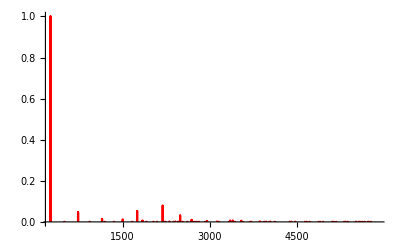

```mathematica
spec@"Plot"[]
```

## Write Up